```mathematica
CompleteConditionalDistribution=ResourceFunction["CompleteConditionalDistribution"];
```

### Utilities

```mathematica
normalArraySample[NormalDistribution[μ_List,σ_List]]:=RandomVariate[NormalDistribution[],Length[μ]]*σ+μ
normalArraySample[n_NormalDistribution]:=RandomVariate@n
```

### Normal mean

μ\[Distributed]Normal(μ_0,σ_0)
y\[Distributed]Normal(μ,σ)

Samples μ with observed y

```mathematica
FullSimplify@CompleteConditionalDistribution[{
μ\[Distributed]NormalDistribution[μ0,σ0],
Table[Indexed[y,i]\[Distributed]NormalDistribution[μ,σ],{i,3}]
},
μ
]
```

NormalDistribution[(μ0 σ^2+σ0^2 (y1+y2+y3))/(σ^2+3 σ0^2),√((σ^2 σ0^2)/(σ^2+3 σ0^2))]

```mathematica
normalNormalMeanSample[NormalDistribution[μ0_,σ0_],σ_,ys_]:=
With[{σn2=(1/σ0^2+Length[ys]/σ^2)^-1},
RandomVariate@NormalDistribution[σn2(μ0/σ0^2+Total[ys]/σ^2),Sqrt[σn2]]
]
```

-Graphics-

### Normal variance

σ^2\[Distributed]InverseGamma(α,β)
y\[Distributed]Normal(μ,σ)

Samples σ^2 with observed y

```mathematica
FullSimplify@CompleteConditionalDistribution[{
σ2\[Distributed]InverseGammaDistribution[α,β],
Table[Indexed[y,i]\[Distributed]NormalDistribution[μ,Sqrt[σ2]],{i,3}]
},
σ2
]
```

InverseGammaDistribution[3/2+α,1/2 (2 β+3 μ^2-2 μ y1+y1^2-2 μ y2+y2^2-2 μ y3+y3^2)]

```mathematica
normalNormalVarianceSample[InverseGammaDistribution[α_,β_],μ_,ys_]:=
RandomVariate@InverseGammaDistribution[α+(1/2)Length[ys],β+(1/2)Total[(ys-μ)^2]]
```

-Graphics-

### Normal regression

x\[Distributed]Normal(μ_0,σ_0)
y\[Distributed]Normal(m*x+b,σ)

Samples x with observed m, b and y

For many observations for the same x:

```mathematica
FullSimplify@CompleteConditionalDistribution[{
x\[Distributed]NormalDistribution[μ0,σ0],
Table[Indexed[y,i]\[Distributed]NormalDistribution[m*x+b,σ],{i,3}]
},
x
]
```

NormalDistribution[(μ0 σ^2-3 b m σ0^2+m σ0^2 (y1+y2+y3))/(σ^2+3 m^2 σ0^2),√((σ^2 σ0^2)/(σ^2+3 m^2 σ0^2))]

```mathematica
normalNormalRegressionSample[NormalDistribution[μ0_,σ0_],σ_,m_,b_,y_]:=
With[{σn2=(1/σ0^2+Total[m^2]/σ^2)^-1},
normalArraySample@NormalDistribution[σn2(μ0/σ0^2+(m.(y-b))/σ^2),Sqrt[σn2]]
]
```

For a vector of x_i:

```mathematica
FullSimplify@CompleteConditionalDistribution[{
x\[Distributed]NormalDistribution[μ0,σ0],
y\[Distributed]NormalDistribution[m*x+b,σ]
},
x
]
```

NormalDistribution[(μ0 σ^2+m (-b+y) σ0^2)/(σ^2+m^2 σ0^2),√((σ^2 σ0^2)/(σ^2+m^2 σ0^2))]

```mathematica
normalNormalRegressionSample[NormalDistribution[μ0_List,σ0_List],σ_,m_,b_,y_]:=
With[{σn2=(1/σ0^2+m^2/σ^2)^-1},
normalArraySample@NormalDistribution[σn2(μ0/σ0^2+(m*(y-b))/σ^2),Sqrt[σn2]]
]
```

https://stmorse.github.io/journal/gibbs.html

-Graphics-

### Time updates

Collecting terms in the formula for the approximate true position, we get that it is linear with t:

```mathematica
Collect[Block[{timeRange={tr1,tr2}},objectDistanceApprox[{p1,p2},t]*l],t]
```

(l (-p1+p2) t)/(-tr1+tr2)+l (p1-((-p1+p2) tr1)/(-tr1+tr2))

Therefore, this can be done with normalNormalRegressionSample with the following values:

m=(l (p2-p1))/(tr2-tr1)
b=l (p1-(tr1 (p2-p1))/(tr2-tr1))

```mathematica
FullSimplify@CompleteConditionalDistribution[{
t\[Distributed]NormalDistribution[μ0,σ0],
c\[Distributed]NormalDistribution[Block[{timeRange={tr1,tr2}},objectDistanceApprox[{p1,p2},t]*l],σ]
},
t
]
```

NormalDistribution[((tr1-tr2)^2 μ0 σ^2+l (p1-p2) (c tr1-l p2 tr1-c tr2+l p1 tr2) σ0^2)/((tr1-tr2)^2 σ^2+l^2 (p1-p2)^2 σ0^2),√(((tr1-tr2)^2 σ^2 σ0^2)/((tr1-tr2)^2 σ^2+l^2 (p1-p2)^2 σ0^2))]

### Beta Bernoulli

p\[Distributed]Beta(α,β)
x\[Distributed]Bernoulli(p)

Samples p with observed x

```mathematica
CompleteConditionalDistribution[{
p\[Distributed]BetaDistribution[α,β],
Table[Indexed[x,i]\[Distributed]BernoulliDistribution[p],{i,3}]
},
p
]
```

BetaDistribution[α+x1+x2+x3,3+β-x1-x2-x3]

```mathematica
betaBernoulliSample[BetaDistribution[α_,β_],xs_]:=
With[{t=Total[xs]},
RandomVariate@BetaDistribution[α+t,β+Length[xs]-t]
]
```

-Graphics-

### Binary normal mixture

m\[Distributed]Bernoulli(p)
x\[Distributed]Piecewise[{{Normal(μ_1,σ_1), m=0}, {Normal(μ_2,σ_2), m=1}}]

Samples m with observed x

```mathematica
logNormalPDF[NormalDistribution[μ_,σ_],x_]:=-(x-μ)^2/(2 σ^2)+1/2 (-Log[2]-Log[π])-Log[σ]
```

```mathematica
logSumExp[m_,level_:0]:=With[{c=Map[Max,m,{level}]},c+Log[Total[Exp[m-c],{level+1}]]]
```

```mathematica
binaryNormalMixtureSample[BernoulliDistribution[p_],n1_NormalDistribution,n2_NormalDistribution,xs_]:=
With[{
mLogProbs=With[{
p1=Log[p]+logNormalPDF[n1,xs],
p2=Log[1-p]+logNormalPDF[n2,xs]},
(*Exp[p1]/(Exp[p1]+Exp[p2])*)
p1-logSumExp[Transpose@{p1,p2},1]
]
},
Boole@MapThread[Greater,{mLogProbs,Log@RandomReal[{0,1},Length[mLogProbs]]}]
]
```

### Piecewise linear normal-normal

The model we want is:

x\[Distributed]Normal(μ_0,σ_0)
y\[Distributed]Normal(f(x),σ)

where f(x) is a piecewise linear function such that:

f(x)=m_i*x+b_i for x∈[l_i,u_i)

We use an equivalent generative process:

x\[Distributed]Normal(μ_0,σ_0)
z\[Distributed]Categorical(cdf(Normal(μ_0,σ_0),u_i)-cdf(Normal(μ_0,σ_0),l_i))
y\[Distributed]Normal(f_z(x),σ)

We marginalize out x to get y\[Conditioned]z as

```mathematica
FullSimplify@Integrate[
PDF[TruncatedDistribution[{l,u},NormalDistribution[μ0,σ0]],x]*
PDF[NormalDistribution[m*x+b,σ],y],
{x,l,u},
GenerateConditions->True,
Assumptions->{l∈Reals,u∈Reals,l<u}
]
```

(ⅇ^(-(b-y+m μ0)^2/(2 (σ^2+m^2 σ0^2))) (-Erf[((l-μ0) σ^2+m (b+l m-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2))]+Erf[((u-μ0) σ^2+m (b+m u-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2))]))/(√(2 π) √(σ^2+m^2 σ0^2) (Erf[(-l+μ0)/(√2 σ0)]-Erf[(-u+μ0)/(√2 σ0)]))

We can then evaluate this for every value of z and normalize to get z\[Conditioned]y. We then sample from this categorical to get z, and then perform the usual normal-normal update sample x.

```mathematica
yGivenZ[NormalDistribution[μ0_,σ0_],σ_,y_,{m_,b_},{l_,u_}]:=
(ⅇ^(-(b-y+m μ0)^2/(2 (σ^2+m^2 σ0^2))) (-Erf[((l-μ0) σ^2+m (b+l m-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2))]+Erf[((u-μ0) σ^2+m (b+m u-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2))]))/(√(2 π) √(σ^2+m^2 σ0^2) (Erf[(-l+μ0)/(√2 σ0)]-Erf[(-u+μ0)/(√2 σ0)]))
```

Compute the log:

```mathematica
PowerExpand@Log[(ⅇ^(-(b-y+m μ0)^2/(2 (σ^2+m^2 σ0^2))) (-Erf[((l-μ0) σ^2+m (b+l m-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2))]+Erf[((u-μ0) σ^2+m (b+m u-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2))]))/(√(2 π) √(σ^2+m^2 σ0^2) (Erf[(-l+μ0)/(√2 σ0)]-Erf[(-u+μ0)/(√2 σ0)]))]
```

-(b-y+m μ0)^2/(2 (σ^2+m^2 σ0^2))+1/2 (-Log[2]-Log[π])-1/2 Log[σ^2+m^2 σ0^2]-Log[Erf[(-l+μ0)/(√2 σ0)]-Erf[(-u+μ0)/(√2 σ0)]]+Log[-Erf[((l-μ0) σ^2+m (b+l m-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2))]+Erf[((u-μ0) σ^2+m (b+m u-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2))]]

```mathematica
logYGivenZ[NormalDistribution[μ0_,σ0_],σ_,y_,{m_,b_},{l_,u_}]:=
-(b-y+m μ0)^2/(2 (σ^2+m^2 σ0^2))+1/2 (-Log[2]-Log[π])-1/2 Log[σ^2+m^2 σ0^2]-(Log[Erf[(-u+μ0)/(√2 σ0),(-l+μ0)/(√2 σ0)]]/.(Indeterminate->-Infinity))+(Log[Erf[((l-μ0) σ^2+m (b+l m-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2)),((u-μ0) σ^2+m (b+m u-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2))]]/.(Indeterminate->-Infinity))
```

### Test case

```mathematica
Needs["AstronomicalDiaries`Astronomy`"]
```

```mathematica
obs=<|"ID"->{"X102611",{1140,1166}},"Object"->Entity["PlanetaryMoon","Moon"],"Relation"->"Below","Reference"->Entity["Star","Hamal"],"Cubits"->Missing[],"Fingers"->Missing[],"Time"->"LastPartOfTheNight","Day"->15,"EarliestDay"->15,"LatestDay"->15,"Month"->"VI","RegnalYear"->{"SE",50},"SEYear"->50,"Date"->DateObject[{-262,9,10},"Day","Julian"],"EarliestDate"->DateObject[{-262,9,10},"Day","Julian"],"LatestDate"->DateObject[{-262,9,10},"Day","Julian"],"Damaged"->True,"Line"->"r 8'","TextID"->"X102611","Range"->{1140,1166},"TimeRange"->{1102,1123},"EarliestDayRange"->{1083,1097},"LatestDayRange"->{1083,1097}|>;
```

```mathematica
intervals=N@Partition[Table[t,{t,-12,12,1}],2,1]
```

{{-12.,-11.},{-11.,-10.},{-10.,-9.},{-9.,-8.},{-8.,-7.},{-7.,-6.},{-6.,-5.},{-5.,-4.},{-4.,-3.},{-3.,-2.},{-2.,-1.},{-1.,0.},{0.,1.},{1.,2.},{2.,3.},{3.,4.},{4.,5.},{5.,6.},{6.,7.},{7.,8.},{8.,9.},{9.,10.},{10.,11.},{11.,12.}}

```mathematica
params=MapThread[
With[{m=(#1[[2]]-#1[[1]])/(#2[[2]]-#2[[1]])},
{m,#1[[1]]-m*#2[[1]]}
]&,
{
Partition[Table[observationDistance[obs,Quantity[t,"Hours"]],{t,-12,12,1}],2,1],
intervals
}
]
```

{{-0.0715901,-6.31287},{-0.0688872,-6.28314},{-0.0607242,-6.20151},{-0.0476096,-6.08348},{-0.0303612,-5.94549},{-0.0100769,-5.8035},{0.0119125,-5.67157},{0.0341098,-5.56058},{0.0549414,-5.47725},{0.0728674,-5.42348},{0.0865045,-5.3962},{0.0947521,-5.38795},{0.0969013,-5.38795},{0.0927129,-5.38377},{0.0824487,-5.36324},{0.0668484,-5.31644},{0.0470575,-5.23727},{0.0245159,-5.12456},{0.000825342,-4.98242},{-0.0223846,-4.81995},{-0.043578,-4.6504},{-0.0614103,-4.48991},{-0.0747998,-4.35602},{-0.0829732,-4.26611}}

```mathematica
Needs["AstronomicalDiaries`Modeling`Utilities`"]
```

```mathematica
allIntervals={intervals,intervals,intervals};
allParams={params,params,params};
y={-5.4,-3.4,3.4};
prior=NormalDistribution[{0.,0.,0.},{1.,1.,1.}];
```

```mathematica
z=1+logPMFSample/@logYGivenZ[prior,0.1,y,Transpose[allParams,{2,3,1}],Transpose[allIntervals,{2,3,1}]]
```

General::munfl: Exp[-876.222] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-928.391] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-867.608] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{4,19,19}

```mathematica
MapThread[Part,{allParams,z}]
```

{{0.0947521,-5.38795},{0.000825342,-4.98242},{0.000825342,-4.98242}}

```mathematica
normalNormalRegressionSample[prior,0.1,MapThread[Part,{allParams,z}][[All,1]],MapThread[Part,{allParams,z}][[All,2]],y]
```

{-3.57383,-2.05429,1.02059}

### Numerical notes

Define some utilities for computing the log erf based on the discussion here:
https://en.wikipedia.org/wiki/Error_function#Bounds_and_Numerical_approximations
of the results from Karagiannidis & Lioumpas (2007):

```mathematica
rawErfc[x_]:=((1-Exp[-1.98*x])*Exp[-x^2])/(1.135*Sqrt[Pi]*x)
```

```mathematica
rawLogErfc[x_]:=-0.698997593858066-x^2+Log[1-ⅇ^(-1.98 x)]-Log[x]
```

These are only good for positive x, and only values greater than about 10:

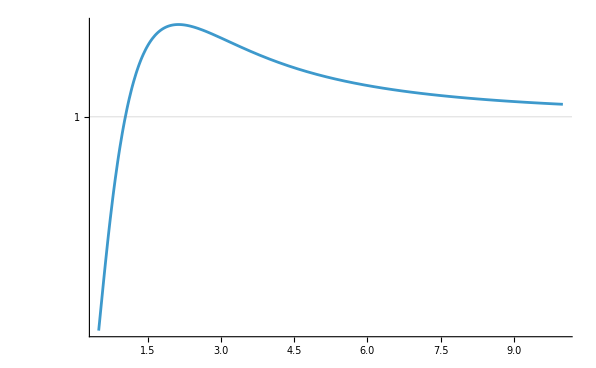

```mathematica
Plot[rawLogErfc[x]/Log@Erfc[SetPrecision[x,10]],{x,0.5,10},PlotRange->All,ScalingFunctions->"Log",PlotRange->All,GridLines->{None,{1}}]
```

### Numerical tools

```mathematica
log1mexp[t_]:=Log[-Internal`Expm1[-t]](*If[t>Log[2],Internal`Log1p[-Exp[-t]],Log[-Internal`Expm1[-t]]]*)
```

```mathematica
Internal`Log1p[-Exp[-60.]]
```

-8.75651×10^-27

```mathematica
logDiffExp[x_,y_]:=x+log1mexp[x-y]
```

```mathematica
logErfc[x_?NumericQ]:=If[Abs[x]<5,Log@Erfc[x],If[Positive[x],rawLogErfc[x],logDiffExp[Log[2],Echo@rawLogErfc[1-x]]]]
```

```mathematica
logErfc[-600.]
```

General::munfl: Exp[-1189.98] is too small to represent as a normalized machine number; precision may be lost.

-361208.

0.693147

```mathematica
Log@Erfc[-6.]
```

0.693147

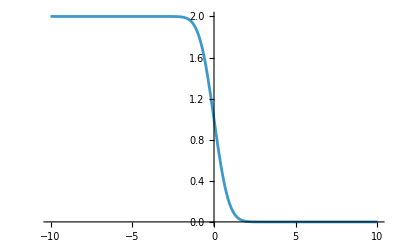

```mathematica
Plot[Erfc[x],{x,-10,10}]
```

```mathematica
logDiffExp[-99.,-100.]
```

-99.4587

```mathematica
logErfc[-60.]
```

-3725.81

General::munfl: Exp[-3726.5] is too small to represent as a normalized machine number; precision may be lost.

0.693147

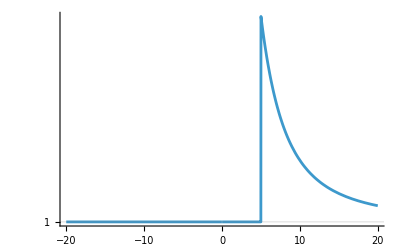

```mathematica
Plot[logErfc[x]/Log@Erfc[SetPrecision[x,10]],{x,-20,20},PlotRange->All,ScalingFunctions->"Log",PlotRange->All,GridLines->{None,{1}}]
```

### WIP

```mathematica
Get["AstronomicalDiaries`Modeling`Utilities`"]
```

```mathematica
Erf[-30.,-31.]
```

General::munfl: Exp[-903.401] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-964.434] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
Erfc[10.]-Erfc[11.]
```

2.08849×10^-45

```mathematica
q[x_]:=1/2*Exp[-0.374x^2-0.777x]
```

```mathematica
logQ[x_]:=-0.777 *x-0.374* x^2-Log[2]
```

```mathematica
logQ[-30.]
```

-313.983

```mathematica
q[-30.]-q[-31]
```

4.35363×10^-137

```mathematica
logQ[-30.]
```

-313.983

```mathematica
N[Log@Erf[-30],100]
```

0.+3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068 ⅈ

```mathematica
N[Erf[-30,-31],100]
```

-2.564656203756111600033397269506039811170997546413105956624442152239703729965260605677628679637367763×10^-393

```mathematica
logQ[0.5]
```

-1.17515

```mathematica
logQ[0.3]
```

-0.959907

```mathematica
CDF[NormalDistribution[],0.5]-CDF[NormalDistribution[],0.3]
```

0.073551

```mathematica
Erf[10.,11.]
```

2.08849×10^-45

```mathematica
N[Log@Erf[-30,-31],1000]
```

```mathematica
Log@Erf[-30.,-31.]
```

General::munfl: Exp[-903.401] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-964.434] is too small to represent as a normalized machine number; precision may be lost.

Indeterminate

```mathematica
logYGivenZ[NormalDistribution[μ0_,σ0_],σ_,y_,{m_,b_},{l_,u_}]:=
-(b-y+m μ0)^2/(2 (σ^2+m^2 σ0^2))+1/2 (-Log[2]-Log[π])-1/2 Log[σ^2+m^2 σ0^2]-(Log[Erf[(-u+μ0)/(√2 σ0),(-l+μ0)/(√2 σ0)]]/.(Indeterminate->-Infinity))+(Log[Erf[((l-μ0) σ^2+m (b+l m-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2)),((u-μ0) σ^2+m (b+m u-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2))]]/.(Indeterminate->-Infinity))
```

```mathematica
(*logYGivenZ[NormalDistribution[μ0_,σ0_],σ_,y_,{m_,b_},{l_,u_}]:=
logSumExp[{
-(b-y+m μ0)^2/(2 (σ^2+m^2 σ0^2)),
-1/2 Log[σ^2+m^2 σ0^2],
-Log[Erf[(-u+μ0)/(√2 σ0),(-l+μ0)/(√2 σ0)]/.(0.->0)],
Log[Erf[((l-μ0) σ^2+m (b+l m-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2)),((u-μ0) σ^2+m (b+m u-y) σ0^2)/(√2 σ σ0 √(σ^2+m^2 σ0^2))]/.(0.->0)]
}]*)
```

```mathematica
logYGivenZ[NormalDistribution[0,1],0.1,-5.4,params[[1]],intervals[[1]]]
```

0.675282

```mathematica
logSumExp[{-Infinity,10.}]
```

10.

```mathematica
logYGivenZ[NormalDistribution[0,1],0.1,-5.4,Transpose@params,Transpose@intervals]
```

{0.675282,-0.370576,-1.69236,-3.01088,-4.01603,-4.44746,-4.17177,-3.23516,-1.86732,-0.42406,0.721821,1.30234,1.19963,0.375084,-1.12719,-3.08075,-5.08826,-6.69863,-7.54237,-7.43457,-6.41747,-4.73494,-2.75745,-0.888558}

```mathematica
logYGivenZ[NormalDistribution[0,1],0.1,{-5.4,-3.4,3.4},Transpose[{params,params,params},{2,3,1}],Transpose[{intervals,intervals,intervals},{2,3,1}]]
```

General::munfl: Exp[-876.069] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-928.232] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-867.459] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{0.675282,-0.370576,-1.69236,-3.01088,-4.01603,-4.44746,-4.17177,-3.23516,-1.86732,-0.42406,0.721821,1.30234,1.19963,0.375084,-1.12719,-3.08075,-5.08826,-6.69863,-7.54237,-7.43457,-6.41747,-4.73494,-2.75745,-0.888558},{-219.801,-234.08,-247.982,-260.151,-268.937,-272.678,-270.761,-263.479,-251.504,-235.87,-217.894,-199.022,-180.646,-163.958,-149.852,-138.871,-131.109,-125.918,-123.039,-123.327,-127.1,-134.289,-144.636,-157.692},{-∞,-∞,-4054.64,-4108.28,-4150.08,-4174.91,-4168.68,-4138.59,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-3535.,-3514.37,-3507.72,-3508.43,-∞,-∞,-∞,-∞}}

```mathematica
logPMFSample@{-∞,-∞,-4054.6362284752176,-4108.278620796701,-4150.07646779111,-4174.911738708126,-4168.684723109227,-4138.586774275186,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-3534.9969900871642,-3514.368494043307,-3507.721582916689,-3508.4276220563697,-∞,-∞,-∞,-∞}
```

23

```mathematica
logYGivenZ[NormalDistribution[0,1],0.1,3.4,Transpose@params,Transpose@intervals]
```

General::munfl: Exp[-876.069] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-928.232] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-867.459] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{-∞,-∞,-4054.64,-4108.28,-4150.08,-4174.91,-4168.68,-4138.59,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-∞,-3535.,-3514.37,-3507.72,-3508.43,-∞,-∞,-∞,-∞}

```mathematica
logYGivenZ2[NormalDistribution[μ0_,σ0_],σ_,y_,{m_,b_},{l_,u_}]:=
Module[{S2,S,α,β,ap,bp},
S2=σ^2+m^2 σ0^2;
S=Sqrt[S2];

α=(l-μ0)/σ0;β=(u-μ0)/σ0;
ap=((l-μ0) σ^2+m (b+l m-y) σ0^2)/(σ σ0 S);
bp=((u-μ0) σ^2+m (b+m u-y) σ0^2)/(σ σ0 S);

-(b-y+m μ0)^2/(2 S2)
-1/2 Log[2 π]
-1/2 Log[S2]
-Log[CDF[NormalDistribution[],β]-CDF[NormalDistribution[],α]]
+Log[CDF[NormalDistribution[],bp]-CDF[NormalDistribution[],ap]]
]
```

```mathematica
normalNormalPiecewiseLinearSample[prior:NormalDistribution[μ0_,σ0_],σ_,y_,params_,intervals_]:=
Module[{zPrior,z,logPMF,pmf},
zPrior=Erf[(μ0-intervals[[All,2]])/(√2 σ0),(μ0-intervals[[All,1]])/(√2 σ0)]/2;
(*zPrior=Log[Function[{l,u},CDF[NormalDistribution[μ0,σ0],u]-CDF[NormalDistribution[μ0,σ0],l]]@@@intervals];*)
z=MapThread[logYGivenZ[prior,σ,y,#1,#2]&,{params,intervals}];
logPMF=z+zPrior;
pmf=Exp@logPMF;
(*If the pmf is just 0s, use the prior*)
pmf=If[Total[pmf]==0,Normalize[Exp[zPrior],Total],Normalize[pmf,Total]];

z=RandomChoice[pmf->Range[Length[pmf]]]
]
```

```mathematica
logYGivenZ[NormalDistribution[0,1],0.1,-5.4,params[[1]],intervals[[1]]]
```

0.675282

```mathematica
logYGivenZ[NormalDistribution[0,1],0.1,-5.4,Transpose@params,Transpose@intervals]
```

{0.675282,-0.370576,-1.69236,-3.01088,-4.01603,-4.44746,-4.17177,-3.23516,-1.86732,-0.42406,0.721821,1.30234,1.19963,0.375084,-1.12719,-3.08075,-5.08826,-6.69863,-7.54237,-7.43457,-6.41747,-4.73494,-2.75745,-0.888558}

```mathematica
logYGivenZ[NormalDistribution[0,1],0.1,{-5.4,-5.4},{Transpose@params,Transpose@params},Transpose@intervals]
```

Thread::tdlen: Objects of unequal length in {-12.,-11.,-10.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.} {{-0.0715818,-0.0688795,-0.0607176,-0.0476044,«16»,-0.0435724,-0.0614032,-0.0747917,-0.0829647},{-«18»,«22»,-«18»}} cannot be combined.

Thread::tdlen: Objects of unequal length in {-0.12,-0.11,-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,«8»,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11}+«1» cannot be combined.

Thread::tdlen: Objects of unequal length in {{-0.0715818,-0.0688795,-0.0607176,-0.0476044,-0.0303578,-0.0100755,0.0119116,«10»,0.0245152,0.000826942,-0.0223809,-0.0435724,-0.0614032,-0.0747917,-0.0829647},«1»} «1» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

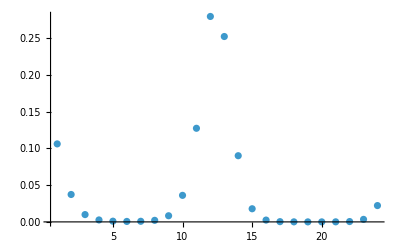

```mathematica
ListPlot[normalNormalPiecewiseLinearZs[NormalDistribution[0,1],0.1,-5.4,params,intervals],PlotRange->All]
```

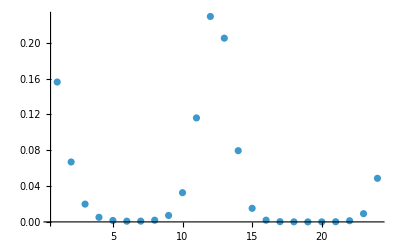

```mathematica
ListPlot[normalNormalPiecewiseLinearZs[NormalDistribution[0,6],0.1,-5.4,params,intervals],PlotRange->All]
```

```mathematica
Needs["AstronomicalDiaries`Modeling`Utilities`"]
```

```mathematica
normalNormalPiecewiseLinearSample[NormalDistribution[0,1],0.1,{-5.4,-2.4},params,intervals]
```

{{0.675282,-476.33},{-0.370576,-497.604},{-1.69236,-518.361},{-3.01088,-536.699},{-4.01603,-550.479},{-4.44746,-556.734},{-4.17177,-554.021},{-3.23513,-543.439},{-1.86601,-526.023},{-0.40266,-503.119},{0.857726,-476.412},{1.64368,-447.891},{1.54098,-419.862},{0.510989,-394.154},{-1.10579,-371.979},{-3.07943,-354.436},{-5.08822,-342.222},{-6.69863,-334.978},{-7.54237,-330.787},{-7.43457,-331.195},{-6.41747,-337.27},{-4.73494,-348.841},{-2.75745,-365.334},{-0.888558,-385.864}}

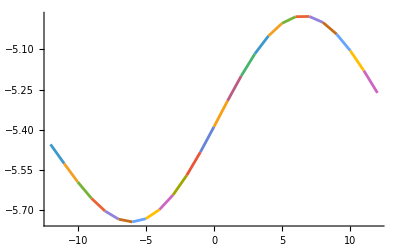

```mathematica
Plot[Evaluate@MapThread[Piecewise[{{#1.{x,1},#2[[1]]<x<#2[[2]]}},Indeterminate]&,{params,intervals}],{x,-12,12}]
```

## OLD

#### Normal mean

-Graphics-

```mathematica
FullSimplify@CompleteConditionalDistribution[{
μ\[Distributed]NormalDistribution[μ0,σ0],
Table[
Indexed[x,i]\[Distributed]NormalDistribution[μ,Sqrt[σ2]],
{i,5}
]
},
μ
]
```

NormalDistribution[(μ0 σ2+σ0^2 (x1+x2+x3+x4+x5))/(5 σ0^2+σ2),√((σ0^2 σ2)/(5 σ0^2+σ2))]

```mathematica
normalNormalMeanSample[NormalDistribution[μ0_,σ0_],σ_,ys_]:=
With[{σn2=(1/σ0^2+Length[ys]/σ^2)^-1},
RandomVariate@NormalDistribution[σn2(μ0/σ0^2+Total[ys]/σ^2),Sqrt[σn2]]
]
```

#### Normal variance

-Graphics-

```mathematica
FullSimplify@CompleteConditionalDistribution[{
σ2\[Distributed]InverseGammaDistribution[α,β],
Table[
Indexed[x,i]\[Distributed]NormalDistribution[μ,Sqrt[σ2]],
{i,5}
]
},
σ2
]
```

InverseGammaDistribution[5/2+α,1/2 (2 β+5 μ^2-2 μ x1+x1^2-2 μ x2+x2^2-2 μ x3+x3^2-2 μ x4+x4^2-2 μ x5+x5^2)]

```mathematica
normalNormalVarianceSample[InverseGammaDistribution[α_,β_],μ_,ys_]:=
RandomVariate@InverseGammaDistribution[α+(1/2)Length[ys],β+(1/2)Total[(ys-μ)^2]]
```

#### Normal regression

https://stmorse.github.io/journal/gibbs.html

-Graphics-

```mathematica
FullSimplify@CompleteConditionalDistribution[{
μ\[Distributed]NormalDistribution[μ0,σ0],
Table[
Indexed[y,i]\[Distributed]NormalDistribution[Indexed[x,i]*μ,σ],
{i,10}
]
},
μ
]
```

NormalDistribution[(μ0 σ^2+σ0^2 (x1 y1+x2 y2+x3 y3+x4 y4+x5 y5+x6 y6+x7 y7+x8 y8+x9 y9+x10 y10))/(σ^2+σ0^2 (x1^2+x2^2+x3^2+x4^2+x5^2+x6^2+x7^2+x8^2+x9^2+x10^2)),√((σ^2 σ0^2)/(σ^2+σ0^2 (x1^2+x2^2+x3^2+x4^2+x5^2+x6^2+x7^2+x8^2+x9^2+x10^2)))]

```mathematica
normalNormalRegressionSample[NormalDistribution[μ0_,σ0_],σ_,xs_,ys_]:=
With[{σn2=(1/σ0^2+Total[xs^2]/σ^2)^-1},
RandomVariate@NormalDistribution[σn2(μ0/σ0^2+(xs.ys)/σ^2),Sqrt[σn2]]
]
```

```mathematica
FullSimplify@CompleteConditionalDistribution[{
x\[Distributed]NormalDistribution[μ0,σ0],
y\[Distributed]NormalDistribution[m*x+b,σ]
},
x
]
```

NormalDistribution[(μ0 σ^2+m (-b+y) σ0^2)/(σ^2+m^2 σ0^2),√((σ^2 σ0^2)/(σ^2+m^2 σ0^2))]

#### Time updates

-Graphics-

```mathematica
Collect[((rangeB-rangeA)/(timeRange[[2]]-timeRange[[1]])*(t-timeRange[[1]])+rangeA)*l,t]
```

l (rangeA+1/2 (-rangeA+rangeB))+1/24 l (-rangeA+rangeB) t

```mathematica
Collect[((or2-or1)/(tr2-tr1)*(t-tr1)+or1)*l,t]
```

(l (-or1+or2) t)/(-tr1+tr2)+l (or1-((-or1+or2) tr1)/(-tr1+tr2))

```mathematica
FullSimplify@CompleteConditionalDistribution[{
t\[Distributed]NormalDistribution[μ0,Sqrt[σ02]],
c\[Distributed]NormalDistribution[((or2-or1)/(tr2-tr1)*(t-tr1)+or1)*l,Sqrt[σ2]]
},
t
]
```

NormalDistribution[(l (or1-or2) (c tr1-l or2 tr1-c tr2+l or1 tr2) σ02+(tr1-tr2)^2 μ0 σ2)/(l^2 (or1-or2)^2 σ02+(tr1-tr2)^2 σ2),√(((tr1-tr2)^2 σ02 σ2)/(l^2 (or1-or2)^2 σ02+(tr1-tr2)^2 σ2))]

```mathematica
FullSimplify@Expand[l (or1-((-or1+or2) tr1)/(-tr1+tr2))]
```

(l (or2 tr1-or1 tr2))/(tr1-tr2)

```mathematica
FullSimplify@CompleteConditionalDistribution[{
t\[Distributed]NormalDistribution[μ0,Sqrt[σ02]],
c\[Distributed]NormalDistribution[t*x+y,Sqrt[σ2]]
},
t
]
```

NormalDistribution[(x (c-y) σ02+μ0 σ2)/(x^2 σ02+σ2),√((σ02 σ2)/(x^2 σ02+σ2))]

```mathematica
With[{
x=(l*(observationDistanceRanges[[All,2]]-observationDistanceRanges[[All,1]]))/(timeRange[[2]]-timeRange[[1]]),
y=(l(observationDistanceRanges[[All,1]]* timeRange[[2]]-observationDistanceRanges[[All,2]]* timeRange[[1]]))/(timeRange[[2]]-timeRange[[1]])
},
{
tμ=(x(c-y)*σ02+μ0*σ2)/(x^2*σ02+σ2),
tσ2=√((σ02 σ2)/(x^2 σ02+σ2))
},
RandomVariate[NormalDistribution[0.,1.],n]*Sqrt[tσ2]+tμ
]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

RandomVariate::array: The array dimensions n given in position 2 of RandomVariate[NormalDistribution[0.,1.],n] should be a list of non-negative machine-sized integers giving the dimensions for the result.

μ0+σ02^(1/4) RandomVariate[NormalDistribution[0.,1.],n]

#### Beta Bernoulli

-Graphics-

```mathematica
FullSimplify@CompleteConditionalDistribution[{
p\[Distributed]BetaDistribution[α,β],
Table[
Indexed[x,i]\[Distributed]BernoulliDistribution[p],
{i,5}
]
},
p
]
```

BetaDistribution[α+x1+x2+x3+x4+x5,5+β-x1-x2-x3-x4-x5]

```mathematica
betaBernoulliSample[BetaDistribution[α_,β_],xs_]:=
With[{t=Total[xs]},
RandomVariate@BetaDistribution[α+t,β+Length[xs]-t]
]
```

#### Binary normal mixture model

```mathematica
logNormalPDF[NormalDistribution[μ_,σ_],x_]:=-(x-μ)^2/(2 σ^2)+1/2 (-Log[2]-Log[π])-Log[σ]
```

```mathematica
logSumExp[m_,level_:0]:=With[{c=Map[Max,m,{level}]},c+Log[Total[Exp[m-c],{level+1}]]]
```

```mathematica
binaryNormalMixtureSample[n1_NormalDistribution,d1_,n2_NormalDistribution,d2_,p_]:=
With[{
mLogProbs=With[{
p1=Log[p]+logNormalPDF[n1,d1],
p2=Log[1-p]+logNormalPDF[n2,d2]},
(*Exp[p1]/(Exp[p1]+Exp[p2])*)
p1-logSumExp[Transpose@{p1,p2},1]
]
},
Boole@MapThread[Greater,{mLogProbs,Log@RandomReal[{0,1},Length[mLogProbs]]}]
]
```